# Synthetic-realistic rain - n = 20

## randrain000,00,0,1,2 → j = 10,20,30,40,50

## Preliminaries

```mathematica
SetDirectory["C:\\Users\\ulzegasi\\Julia_files\\ParInf_HMC"]
Needs["CustomTicks`"]
Needs["ErrorBarPlots`"]
```

C:\Users\ulzegasi\Julia_files\ParInf_HMC

```mathematica
indatdir="C:\\Users\\ulzegasi\\Julia_files\\ParInf_HMC\\input_data";
```

## Parameters

```mathematica
tdat=Import["t.dat"][[Range[2,5002],2]];

n=20 ;                             (* n+1 -> "end point" beads (see Tuckerman'93), n -> number of segments *)
j=30;                             (* j-1 staging beads between measurement points *)
N temp=n*1000+1; (* Total number of points in a system realization to generate synthetic data *)
Np=n*j+1;


t temp=Array[#&,N temp,{First[tdat],Last[tdat]}]; (* Generate N time points in[t[1],t[end]] *)
t=Array[#&,Np,{First[tdat],Last[tdat]}]; 
T=Last[tdat]-First[tdat];                                       (* Total time interval *)
dt temp=T/(N temp-1) ;                                                       (* Time step *)
dt=T/(Np-1);
ty temp=Round[Array[#&,n+1,{1,N temp}]];                 (* Indeces of "boundary" beads (=measurement points) *)
ty=Round[Array[#&,n+1,{1,Np}]];                                    (* t temp[[ty temp]] and ty[[ty]] should coincide *)
counter=0;Do[If[t temp[[ty temp[[i]]]]!=t[[ty[[i]]]],counter+=1],{i,1,Length[ty]}];
If[counter>0,Print["Be careful, indeces of boundary beads do not coincide!"]]
```

```mathematica
K=50.;    (* Retention time *)
γ=0.2;    (* Dimensionless noise parameter *)
σ=0.10; (* Measurement noise *)
S=ConstantArray[0.0,N temp];    (* System realization (with true parameters) *)
St=ConstantArray[0.0,{N temp,2}];  (* System realization with time *)
```

## Generate rain

```mathematica
r=Transpose[{t[[ty]],(Sin[t[[ty]]/100.]^2+0.1)*RandomVariate[NormalDistribution[0,2],n+1]^2}];    
counter=0;Do[If[r[[i,2]]≤0,counter+=1],{i,1,Length[r]}];
If[counter>0,Print["Be careful, negative or zero rain!"],Print["Rain is > 0. Ok"]] (* check that rain is non-zero*)
```

Rain is > 0. Ok

```mathematica
r
```

{{0.166667,0.0853996},{41.8333,0.11933},{83.5,2.89853},{125.167,0.143872},{166.833,12.0251},{208.5,1.92157},{250.167,0.873637},{291.833,0.185714},{333.5,2.67574},{375.167,1.95261},{416.833,4.37012},{458.5,0.293069},{500.167,8.93676},{541.833,1.20671},{583.5,0.623885},{625.167,0.217365},{666.833,1.36264},{708.5,0.837644},{750.167,7.62808},{791.833,8.23136},{833.5,5.06155}}

```mathematica
r={{0.166666666666667,0.08539963706013345},{41.833333333333336,0.11932983160669647},{83.50000000000001,2.8985339836961486},{125.16666666666669,0.14387214404604787},{166.83333333333334,12.025081786508403},{208.50000000000003,1.9215723089115686},{250.16666666666669,0.8736367864874934},{291.83333333333337,0.18571366739987927},{333.50000000000006,2.6757405950577517},{375.16666666666674,1.9526064283870157},{416.8333333333334,4.370123680690697},{458.50000000000006,0.29306941914784296},{500.16666666666674,8.936759351626346},{541.8333333333334,1.2067083582143392},{583.5,0.6238849804303727},{625.1666666666667,0.21736533131681746},{666.8333333333334,1.3626374340920933},{708.5,0.8376441400549063},{750.1666666666667,7.628084392207564},{791.8333333333334,8.23136287096145},{833.5000000000001,5.061545197179079}};
```

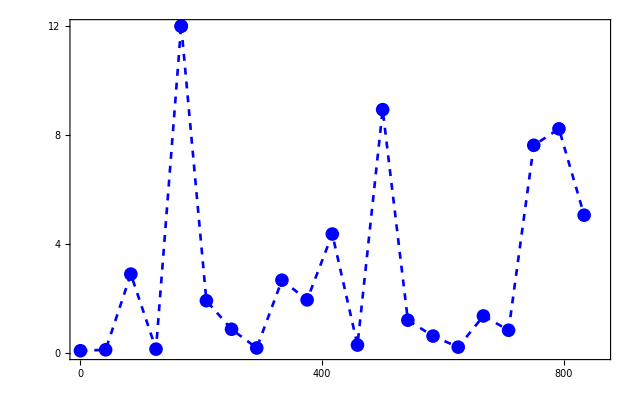

```mathematica
ListPlot[r,Joined->True,AxesOrigin->{0,0},PlotMarkers->{"●",14},PlotStyle->Directive[Thickness[0.003],Dashed,Blue],PlotRange->{{0,860},{0,12}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,2000,400,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,30,2,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotRange->{All,{-5,30}}]
```

## Smoothing and interpolating the rain

```mathematica
rIntRaw=Interpolation[r,InterpolationOrder->1];  (* Interpolation of the raw rain data *)
```

Rain is > 0. Ok

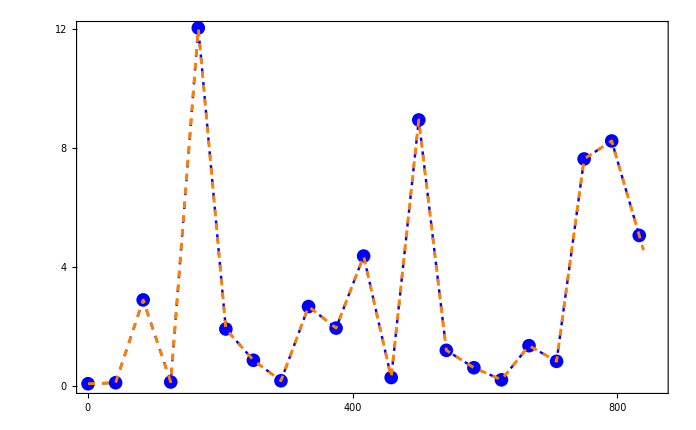

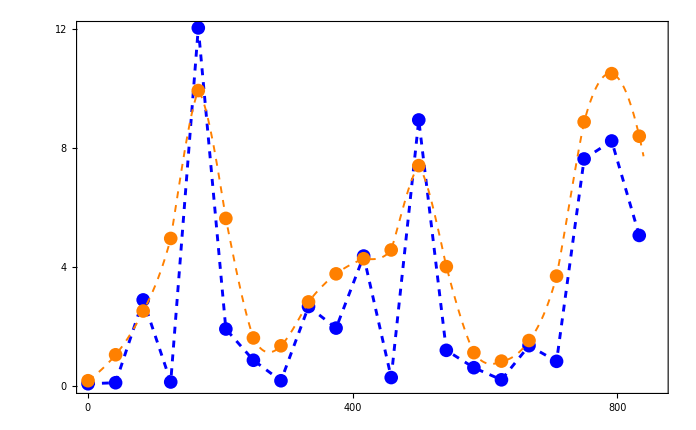

```mathematica
r2=r[[All,2]];
rSmooth=Transpose[{t[[ty]],2.0*LowpassFilter[r2,1.2]}];
counter=0;Do[If[rSmooth[[i,2]]≤0,counter+=1],{i,1,Length[rSmooth]}];
If[counter>0,Print["Be careful, negative or zero rain!"],Print["Rain is > 0. Ok"]] (* check that rain is non-zero*)

rInt=Interpolation[rSmooth,InterpolationOrder->3];  (* Interpolation of the smoothed rain *)

Show[
ListPlot[r,Joined->True,AxesOrigin->{0,0},PlotMarkers->{"●",14},PlotStyle->Directive[Thickness[0.0025],Dashed,Blue],PlotRange->{All,All}],

Plot[rIntRaw[x],{x,0.17,840},PlotStyle->{Dashed,Orange,Thickness[0.003]},PlotRange->All],

PlotRange->{{0,860},{0,12}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,2000,400,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,30,2,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}
]

Show[
ListPlot[r,Joined->True,AxesOrigin->{0,0},PlotMarkers->{"●",14},PlotStyle->Directive[Thickness[0.003],Dashed,Blue],PlotRange->{All,All}],

ListPlot[rSmooth,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",14},PlotStyle->Directive[Thickness[0.003],Dashed,Orange],PlotRange->{{0,860},{0,10}},PlotRange->{All,All}],

Plot[rInt[x],{x,0.17,840},PlotStyle->{Dashed,Orange,Thickness[0.002]},PlotRange->All],

PlotRange->{{0,860},{0,12}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,2000,400,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,30,2,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}
]
```

## Generate “extended” rain data including staging points Choose smoothed OR raw rain

### Smoothed rain

```mathematica
(* Here we use the 3rd-order interpolation of the smoothed rain data *)
(* to generate a large table of N temp points. *)
(* This will be used below to generate a system realization and the corresponding synthetic data points y *)
rExtExt=Table[{x,rInt[x]},{x,t temp}];  
counter=0;Do[If[rExtExt[[i,2]]≤0,counter+=1],{i,1,Length[rExtExt]}];
If[counter>0,Print["Be careful, negative or zero rain!"],Print["Rain is > 0. Ok"]] (* check that rain is non-zero*)
Length[rExtExt]
```

Rain is > 0. Ok

20001

```mathematica
(* Here we use the 3rd-order interpolation of the smoothed rain data *)
(* to generate a smaller table of N points. This will be used in the Julia code.*)
rExt=Table[{x,rInt[x]},{x,t}];
counter=0;Do[If[rExt[[i,2]]≤0,counter+=1],{i,1,Length[rExt]}];
If[counter>0,Print["Be careful, negative or zero rain!"],Print["Rain is > 0. Ok"]] (* check that rain is non-zero*)
Length[rExt]
```

Rain is > 0. Ok

201

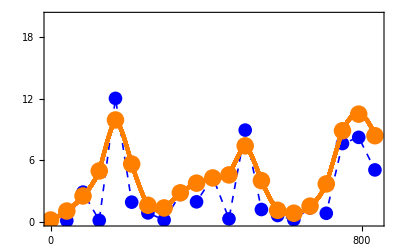

```mathematica
Show[
ListPlot[r,Joined->True,AxesOrigin->{0,0},PlotMarkers->{"●",14},PlotStyle->Directive[Thickness[0.003],Dashed,Blue],PlotRange->{All,All}],

ListPlot[rSmooth,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",18},PlotStyle->Directive[Thickness[0.003],Dashed,Orange],PlotRange->{{0,840},{0,10}},PlotRange->{All,All}],
(*Plot[rInt[x],{x,0.17,1667},PlotStyle->{Dashed,Orange,Thickness[0.01]},PlotRange->All],*)

ListPlot[rExtExt,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",4},PlotStyle->Directive[Thickness[0.003],Dashed,Orange],PlotRange->{{0,840},{0,10}},PlotRange->{All,All}],

PlotRange->{{0,840},{0,20}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,2000,400,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,30,2,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}
]
```

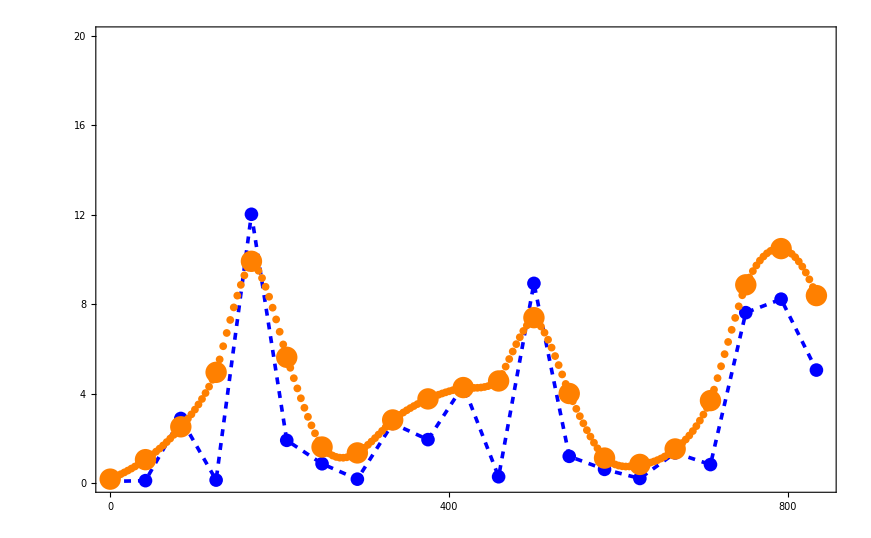

```mathematica
Show[
ListPlot[r,Joined->True,AxesOrigin->{0,0},PlotMarkers->{"●",14},PlotStyle->Directive[Thickness[0.003],Dashed,Blue],PlotRange->{All,All}],

ListPlot[rSmooth,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",22},PlotStyle->Directive[Thickness[0.003],Dashed,Orange],PlotRange->{{0,840},{0,10}},PlotRange->{All,All}],
(*Plot[rInt[x],{x,0.17,1667},PlotStyle->{Orange,Thickness[0.003]},PlotRange->All],*)

ListPlot[rExt,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",8},PlotStyle->Directive[Thickness[0.003],Dashed,Orange],PlotRange->{{0,840},{0,10}},PlotRange->{All,All}],

PlotRange->{{0,840},{0,20}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,2000,400,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,30,2,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}
]
```

### Raw rain

```mathematica
(* Here we use the linear interpolation of the raw rain data *)
(* to generate a large table of N temp points. *)
(* This will be used below to generate a system realization and the corresponding synthetic data points y *)
rExtExt=Table[{x,rIntRaw[x]},{x,t temp}];  
counter=0;Do[If[rExtExt[[i,2]]≤0,counter+=1],{i,1,Length[rExtExt]}];
If[counter>0,Print["Be careful, negative or zero rain!"],Print["Rain is > 0. Ok"]] (* check that rain is non-zero*)
Length[rExtExt]
```

Rain is > 0. Ok

20001

```mathematica
(* Here we use the linear interpolation of the raw rain data *)
(* to generate a smaller table of N points. This will be used in the Julia code.*)
rExt=Table[{x,rIntRaw[x]},{x,t}];
counter=0;Do[If[rExt[[i,2]]≤0,counter+=1],{i,1,Length[rExt]}];
If[counter>0,Print["Be careful, negative or zero rain!"],Print["Rain is > 0. Ok"]] (* check that rain is non-zero*)
Length[rExt]
```

Rain is > 0. Ok

601

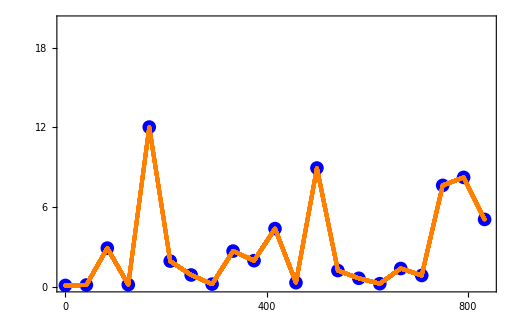

```mathematica
Show[
ListPlot[r,Joined->True,AxesOrigin->{0,0},PlotMarkers->{"●",14},PlotStyle->Directive[Thickness[0.003],Dashed,Blue],PlotRange->{All,All}],

(*ListPlot[rSmooth,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",18},PlotStyle->Directive[Thickness[0.003],Dashed,Orange],PlotRange->{{0,840},{0,10}},PlotRange->{All,All}],*)
(*Plot[rInt[x],{x,0.17,1667},PlotStyle->{Dashed,Orange,Thickness[0.01]},PlotRange->All],*)

ListPlot[rExtExt,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",4},PlotStyle->Directive[Thickness[0.003],Dashed,Orange],PlotRange->{{0,840},{0,10}},PlotRange->{All,All}],

PlotRange->{{0,840},{0,20}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,2000,400,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,30,2,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}
]
```

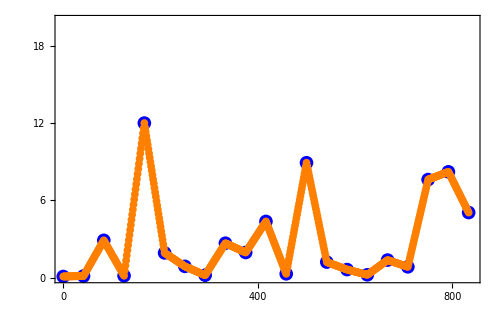

```mathematica
Show[
ListPlot[r,Joined->True,AxesOrigin->{0,0},PlotMarkers->{"●",14},PlotStyle->Directive[Thickness[0.003],Dashed,Blue],PlotRange->{All,All}],

(*ListPlot[rSmooth,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",22},PlotStyle->Directive[Thickness[0.003],Dashed,Orange],PlotRange->{{0,840},{0,10}},PlotRange->{All,All}],*)
(*Plot[rInt[x],{x,0.17,1667},PlotStyle->{Orange,Thickness[0.003]},PlotRange->All],*)

ListPlot[rExt,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",8},PlotStyle->Directive[Thickness[0.003],Dashed,Orange],PlotRange->{{0,840},{0,10}},PlotRange->{All,All}],

PlotRange->{{0,840},{0,20}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,2000,400,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,30,2,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}
]
```

## Generate a system realization and synthetic runoff data

```mathematica
S[[1]]={t temp[[1]],K*rExtExt[[1,2]]}
```

{0.166667,4.26998}

```mathematica
Do[S[[i]]={t temp[[i]],S[[i-1,2]]+(dt temp)*(rExtExt[[i-1,2]]-S[[i-1,2]]/K)+Sqrt[dt temp]*Sqrt[γ/K]*S[[i-1,2]]*RandomVariate[NormalDistribution[]]}
,{i,2,N temp}]
```

```mathematica
bq=Log[(1/K)*(S[[ty temp,2]]/rExtExt[[ty temp,2]])]+σ*RandomVariate[NormalDistribution[],n+1];
y=rExtExt[[ty temp,2]]*Exp[bq];

yerr=Table[{{t[[ty[[i]]]],y[[i]]},ErrorBar[2*σ*y[[i]]]},{i,1,Length[y]}];
```

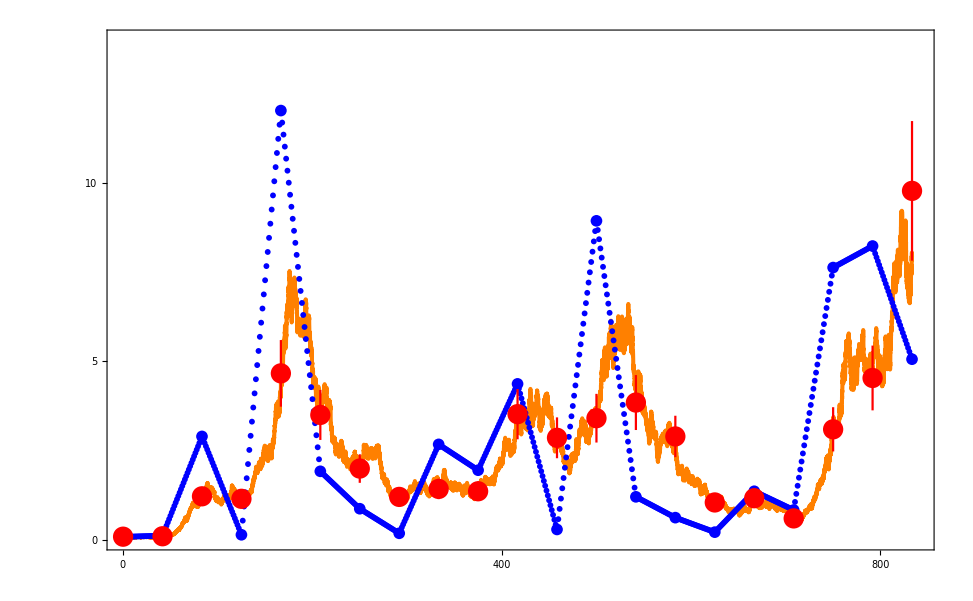

```mathematica
Show[
ListPlot[Transpose[{t temp,S[[All,2]]/K}],Joined->True,AxesOrigin->{0,0},PlotStyle->Directive[Thickness[0.003],Orange],PlotRange->{All,All}],

ListPlot[rExt,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",6},PlotStyle->Directive[Thickness[0.003],Dashed,Blue],PlotRange->{{0,840},{0,10}},PlotRange->{All,All}],

ListPlot[r,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",12},PlotStyle->Directive[Thickness[0.003],Dashed,Blue],PlotRange->{All,All}],
(*Plot[rInt[x],{x,0.17,1667},PlotStyle->{Dashed,Orange,Thickness[0.01]},PlotRange->All],*)

ErrorListPlot[yerr,AxesOrigin->{0,0},PlotStyle->Directive[PointSize[0.015],Red],PlotRange->{{0,1800},{0,10}},PlotRange->{All,All}],

PlotRange->{{0,840},{0,14}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,2000,400,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,50,5,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}
]
```

## Export data

```mathematica
St[[All,1]]=S[[All,2]];
St[[All,2]]=t temp;
```

```mathematica
Export[indatdir<>"\\St_randrainR0.dat",St]
Export[indatdir<>"\\bq_randrainR0.dat",bq]
Export[indatdir<>"\\y_randrainR0.dat",y]
Export[indatdir<>"\\r_randrainR0.dat",r]
Export[indatdir<>"\\rExt_randrainR0.dat",rExt]
```

C:\Users\ulzegasi\Julia_files\ParInf_HMC\input_data\St_randrainR0.dat

C:\Users\ulzegasi\Julia_files\ParInf_HMC\input_data\bq_randrainR0.dat

C:\Users\ulzegasi\Julia_files\ParInf_HMC\input_data\y_randrainR0.dat

C:\Users\ulzegasi\Julia_files\ParInf_HMC\input_data\r_randrainR0.dat

C:\Users\ulzegasi\Julia_files\ParInf_HMC\input_data\rExt_randrainR0.dat

# Synthetic-realistic rain - n = 10

## randrain000,00,0,1,2 → j = 10,20,30,40,50

## Preliminaries

```mathematica
SetDirectory["C:\\Users\\ulzegasi\\Julia_files\\ParInf_HMC"]
Needs["CustomTicks`"]
Needs["ErrorBarPlots`"]
```

C:\Users\ulzegasi\Julia_files\ParInf_HMC

```mathematica
indatdir="C:\\Users\\ulzegasi\\Julia_files\\ParInf_HMC\\input_data";
```

## Parameters

```mathematica
tdat=Import["t.dat"][[Range[2,5002],2]];

n=10 ;                             (* n+1 -> "end point" beads (see Tuckerman'93), n -> number of segments *)
j=30;                             (* j-1 staging beads between measurement points *)
N temp=n*1000+1; (* Total number of points in a system realization to generate synthetic data *)
Np=n*j+1;


t temp=Array[#&,N temp,{First[tdat],Last[tdat]}]; (* Generate N time points in[t[1],t[end]] *)
t=Array[#&,Np,{First[tdat],Last[tdat]}]; 
T=Last[tdat]-First[tdat];                                       (* Total time interval *)
dt temp=T/(N temp-1) ;                                                       (* Time step *)
dt=T/(Np-1);
ty temp=Round[Array[#&,n+1,{1,N temp}]];                 (* Indeces of "boundary" beads (=measurement points) *)
ty=Round[Array[#&,n+1,{1,Np}]];                                    (* t temp[[ty temp]] and ty[[ty]] should coincide *)
counter=0;Do[If[t temp[[ty temp[[i]]]]!=t[[ty[[i]]]],counter+=1],{i,1,Length[ty]}];
If[counter>0,Print["Be careful, indeces of boundary beads do not coincide!"]]
```

```mathematica
K=50.;    (* Retention time *)
γ=0.2;    (* Dimensionless noise parameter *)
σ=0.10; (* Measurement noise *)
S=ConstantArray[0.0,N temp];    (* System realization (with true parameters) *)
St=ConstantArray[0.0,{N temp,2}];  (* System realization with time *)
```

## Generate rain

```mathematica
r=Transpose[{t[[ty]],(Sin[t[[ty]]/100.]^2+0.1)*RandomVariate[NormalDistribution[0,2],n+1]^2}];    
counter=0;Do[If[r[[i,2]]≤0,counter+=1],{i,1,Length[r]}];
If[counter>0,Print["Be careful, negative or zero rain!"],Print["Rain is > 0. Ok"]] (* check that rain is non-zero*)
```

Rain is > 0. Ok

```mathematica
r
```

{{0.166667,0.0853996},{41.8333,0.11933},{83.5,2.89853},{125.167,0.143872},{166.833,12.0251},{208.5,1.92157},{250.167,0.873637},{291.833,0.185714},{333.5,2.67574},{375.167,1.95261},{416.833,4.37012},{458.5,0.293069},{500.167,8.93676},{541.833,1.20671},{583.5,0.623885},{625.167,0.217365},{666.833,1.36264},{708.5,0.837644},{750.167,7.62808},{791.833,8.23136},{833.5,5.06155}}

```mathematica
r={{0.166666666666667,0.08539963706013345},{41.833333333333336,0.11932983160669647},{83.50000000000001,2.8985339836961486},{125.16666666666669,0.14387214404604787},{166.83333333333334,12.025081786508403},{208.50000000000003,1.9215723089115686},{250.16666666666669,0.8736367864874934},{291.83333333333337,0.18571366739987927},{333.50000000000006,2.6757405950577517},{375.16666666666674,1.9526064283870157},{416.8333333333334,4.370123680690697},{458.50000000000006,0.29306941914784296},{500.16666666666674,8.936759351626346},{541.8333333333334,1.2067083582143392},{583.5,0.6238849804303727},{625.1666666666667,0.21736533131681746},{666.8333333333334,1.3626374340920933},{708.5,0.8376441400549063},{750.1666666666667,7.628084392207564},{791.8333333333334,8.23136287096145},{833.5000000000001,5.061545197179079}};
```

```mathematica
r =Table[r[[i]],{i,1,Length[r],2}]
```

{{0.166667,0.0853996},{83.5,2.89853},{166.833,12.0251},{250.167,0.873637},{333.5,2.67574},{416.833,4.37012},{500.167,8.93676},{583.5,0.623885},{666.833,1.36264},{750.167,7.62808},{833.5,5.06155}}

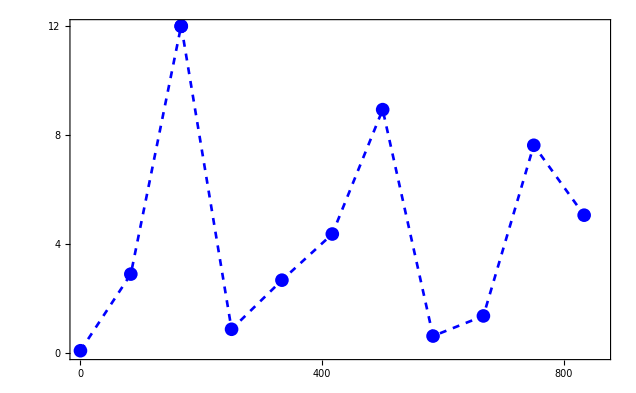

```mathematica
ListPlot[r,Joined->True,AxesOrigin->{0,0},PlotMarkers->{"●",14},PlotStyle->Directive[Thickness[0.003],Dashed,Blue],PlotRange->{{0,860},{0,12}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,2000,400,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,30,2,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None},PlotRange->{All,{-5,30}}]
```

## Smoothing and interpolating the rain

```mathematica
rIntRaw=Interpolation[r,InterpolationOrder->1];  (* Interpolation of the raw rain data *)
```

Rain is > 0. Ok

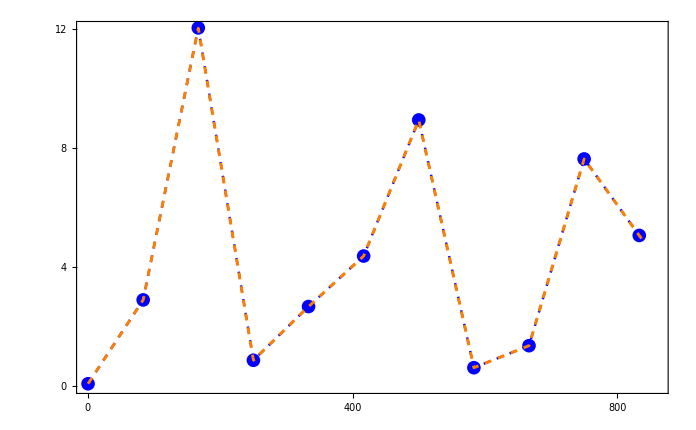

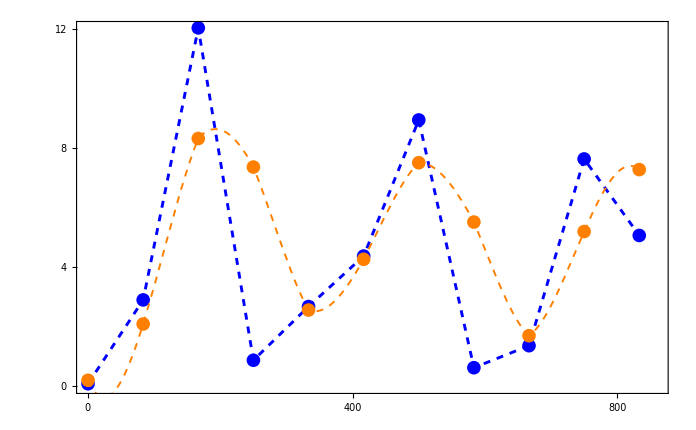

```mathematica
r2=r[[All,2]];
rSmooth=Transpose[{t[[ty]],2.0*LowpassFilter[r2,1.2]}];
counter=0;Do[If[rSmooth[[i,2]]≤0,counter+=1],{i,1,Length[rSmooth]}];
If[counter>0,Print["Be careful, negative or zero rain!"],Print["Rain is > 0. Ok"]] (* check that rain is non-zero*)

rInt=Interpolation[rSmooth,InterpolationOrder->3];  (* Interpolation of the smoothed rain *)

Show[
ListPlot[r,Joined->True,AxesOrigin->{0,0},PlotMarkers->{"●",14},PlotStyle->Directive[Thickness[0.0025],Dashed,Blue],PlotRange->{All,All}],

Plot[rIntRaw[x],{x,0.17,840},PlotStyle->{Dashed,Orange,Thickness[0.003]},PlotRange->All],

PlotRange->{{0,860},{0,12}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,2000,400,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,30,2,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}
]

Show[
ListPlot[r,Joined->True,AxesOrigin->{0,0},PlotMarkers->{"●",14},PlotStyle->Directive[Thickness[0.003],Dashed,Blue],PlotRange->{All,All}],

ListPlot[rSmooth,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",14},PlotStyle->Directive[Thickness[0.003],Dashed,Orange],PlotRange->{{0,860},{0,10}},PlotRange->{All,All}],

Plot[rInt[x],{x,0.17,840},PlotStyle->{Dashed,Orange,Thickness[0.002]},PlotRange->All],

PlotRange->{{0,860},{0,12}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,2000,400,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,30,2,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}
]
```

## Generate “extended” rain data including staging points Choose smoothed OR raw rain

### Smoothed rain

```mathematica
(* Here we use the 3rd-order interpolation of the smoothed rain data *)
(* to generate a large table of N temp points. *)
(* This will be used below to generate a system realization and the corresponding synthetic data points y *)
rExtExt=Table[{x,rInt[x]},{x,t temp}];  
counter=0;Do[If[rExtExt[[i,2]]≤0,counter+=1],{i,1,Length[rExtExt]}];
If[counter>0,Print["Be careful, negative or zero rain!"],Print["Rain is > 0. Ok"]] (* check that rain is non-zero*)
Length[rExtExt]
```

Rain is > 0. Ok

20001

```mathematica
(* Here we use the 3rd-order interpolation of the smoothed rain data *)
(* to generate a smaller table of N points. This will be used in the Julia code.*)
rExt=Table[{x,rInt[x]},{x,t}];
counter=0;Do[If[rExt[[i,2]]≤0,counter+=1],{i,1,Length[rExt]}];
If[counter>0,Print["Be careful, negative or zero rain!"],Print["Rain is > 0. Ok"]] (* check that rain is non-zero*)
Length[rExt]
```

Rain is > 0. Ok

201

```mathematica
Show[
ListPlot[r,Joined->True,AxesOrigin->{0,0},PlotMarkers->{"●",14},PlotStyle->Directive[Thickness[0.003],Dashed,Blue],PlotRange->{All,All}],

ListPlot[rSmooth,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",18},PlotStyle->Directive[Thickness[0.003],Dashed,Orange],PlotRange->{{0,840},{0,10}},PlotRange->{All,All}],
(*Plot[rInt[x],{x,0.17,1667},PlotStyle->{Dashed,Orange,Thickness[0.01]},PlotRange->All],*)

ListPlot[rExtExt,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",4},PlotStyle->Directive[Thickness[0.003],Dashed,Orange],PlotRange->{{0,840},{0,10}},PlotRange->{All,All}],

PlotRange->{{0,840},{0,20}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,2000,400,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,30,2,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}
]
```

-Graphics-

```mathematica
Show[
ListPlot[r,Joined->True,AxesOrigin->{0,0},PlotMarkers->{"●",14},PlotStyle->Directive[Thickness[0.003],Dashed,Blue],PlotRange->{All,All}],

ListPlot[rSmooth,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",22},PlotStyle->Directive[Thickness[0.003],Dashed,Orange],PlotRange->{{0,840},{0,10}},PlotRange->{All,All}],
(*Plot[rInt[x],{x,0.17,1667},PlotStyle->{Orange,Thickness[0.003]},PlotRange->All],*)

ListPlot[rExt,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",8},PlotStyle->Directive[Thickness[0.003],Dashed,Orange],PlotRange->{{0,840},{0,10}},PlotRange->{All,All}],

PlotRange->{{0,840},{0,20}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,2000,400,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,30,2,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}
]
```

-Graphics-

### Raw rain

```mathematica
(* Here we use the linear interpolation of the raw rain data *)
(* to generate a large table of N temp points. *)
(* This will be used below to generate a system realization and the corresponding synthetic data points y *)
rExtExt=Table[{x,rIntRaw[x]},{x,t temp}];  
counter=0;Do[If[rExtExt[[i,2]]≤0,counter+=1],{i,1,Length[rExtExt]}];
If[counter>0,Print["Be careful, negative or zero rain!"],Print["Rain is > 0. Ok"]] (* check that rain is non-zero*)
Length[rExtExt]
```

Rain is > 0. Ok

10001

```mathematica
(* Here we use the linear interpolation of the raw rain data *)
(* to generate a smaller table of N points. This will be used in the Julia code.*)
rExt=Table[{x,rIntRaw[x]},{x,t}];
counter=0;Do[If[rExt[[i,2]]≤0,counter+=1],{i,1,Length[rExt]}];
If[counter>0,Print["Be careful, negative or zero rain!"],Print["Rain is > 0. Ok"]] (* check that rain is non-zero*)
Length[rExt]
```

Rain is > 0. Ok

301

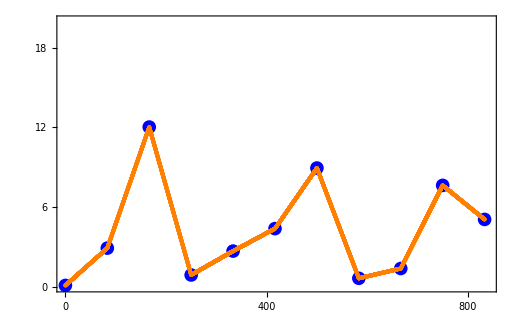

```mathematica
Show[
ListPlot[r,Joined->True,AxesOrigin->{0,0},PlotMarkers->{"●",14},PlotStyle->Directive[Thickness[0.003],Dashed,Blue],PlotRange->{All,All}],

(*ListPlot[rSmooth,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",18},PlotStyle->Directive[Thickness[0.003],Dashed,Orange],PlotRange->{{0,840},{0,10}},PlotRange->{All,All}],*)
(*Plot[rInt[x],{x,0.17,1667},PlotStyle->{Dashed,Orange,Thickness[0.01]},PlotRange->All],*)

ListPlot[rExtExt,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",4},PlotStyle->Directive[Thickness[0.003],Dashed,Orange],PlotRange->{{0,840},{0,10}},PlotRange->{All,All}],

PlotRange->{{0,840},{0,20}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,2000,400,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,30,2,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}
]
```

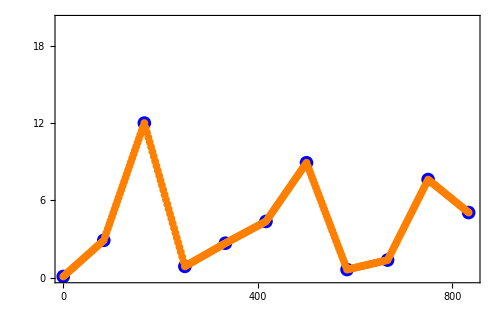

```mathematica
Show[
ListPlot[r,Joined->True,AxesOrigin->{0,0},PlotMarkers->{"●",14},PlotStyle->Directive[Thickness[0.003],Dashed,Blue],PlotRange->{All,All}],

(*ListPlot[rSmooth,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",22},PlotStyle->Directive[Thickness[0.003],Dashed,Orange],PlotRange->{{0,840},{0,10}},PlotRange->{All,All}],*)
(*Plot[rInt[x],{x,0.17,1667},PlotStyle->{Orange,Thickness[0.003]},PlotRange->All],*)

ListPlot[rExt,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",8},PlotStyle->Directive[Thickness[0.003],Dashed,Orange],PlotRange->{{0,840},{0,10}},PlotRange->{All,All}],

PlotRange->{{0,840},{0,20}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,2000,400,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,30,2,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}
]
```

## Generate a system realization and synthetic runoff data

```mathematica
S[[1]]={t temp[[1]],K*rExtExt[[1,2]]}
```

{0.166667,4.26998}

```mathematica
Do[S[[i]]={t temp[[i]],S[[i-1,2]]+(dt temp)*(rExtExt[[i-1,2]]-S[[i-1,2]]/K)+Sqrt[dt temp]*Sqrt[γ/K]*S[[i-1,2]]*RandomVariate[NormalDistribution[]]}
,{i,2,N temp}]
```

```mathematica
bq=Log[(1/K)*(S[[ty temp,2]]/rExtExt[[ty temp,2]])]+σ*RandomVariate[NormalDistribution[],n+1];
y=rExtExt[[ty temp,2]]*Exp[bq];

yerr=Table[{{t[[ty[[i]]]],y[[i]]},ErrorBar[2*σ*y[[i]]]},{i,1,Length[y]}];
```

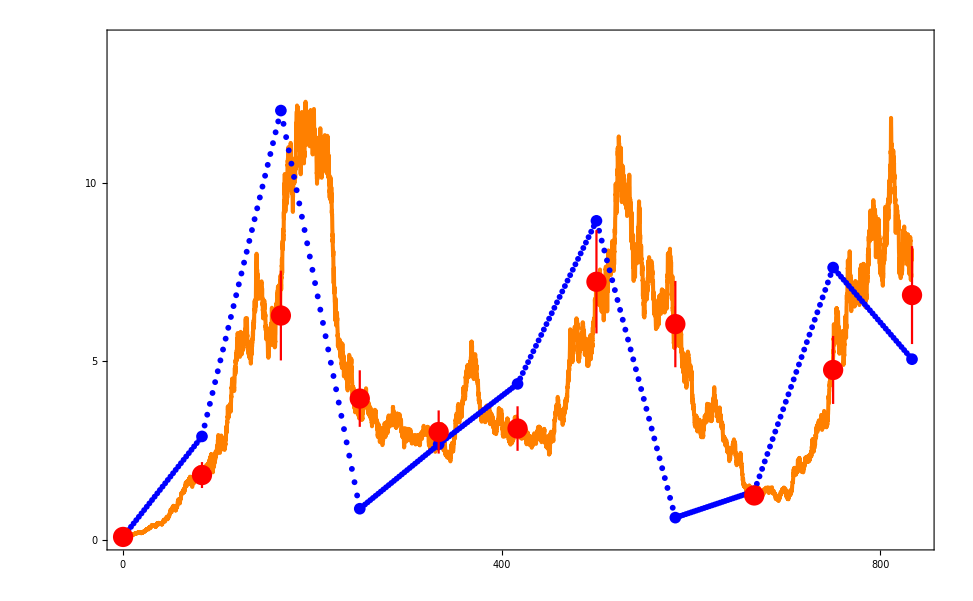

```mathematica
Show[
ListPlot[Transpose[{t temp,S[[All,2]]/K}],Joined->True,AxesOrigin->{0,0},PlotStyle->Directive[Thickness[0.003],Orange],PlotRange->{All,All}],

ListPlot[rExt,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",6},PlotStyle->Directive[Thickness[0.003],Dashed,Blue],PlotRange->{{0,840},{0,10}},PlotRange->{All,All}],

ListPlot[r,Joined->False,AxesOrigin->{0,0},PlotMarkers->{"●",12},PlotStyle->Directive[Thickness[0.003],Dashed,Blue],PlotRange->{All,All}],
(*Plot[rInt[x],{x,0.17,1667},PlotStyle->{Dashed,Orange,Thickness[0.01]},PlotRange->All],*)

ErrorListPlot[yerr,AxesOrigin->{0,0},PlotStyle->Directive[PointSize[0.015],Red],PlotRange->{{0,1800},{0,10}},PlotRange->{All,All}],

PlotRange->{{0,840},{0,14}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,2000,400,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,50,5,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}
]
```

## Export data

```mathematica
St[[All,1]]=S[[All,2]];
St[[All,2]]=t temp;
```

```mathematica
Export[indatdir<>"\\St_randrainR0n10.dat",St]
Export[indatdir<>"\\bq_randrainR0n10.dat",bq]
Export[indatdir<>"\\y_randrainR0n10.dat",y]
Export[indatdir<>"\\r_randrainR0n10.dat",r]
Export[indatdir<>"\\rExt_randrainR0n10.dat",rExt]
```

C:\Users\ulzegasi\Julia_files\ParInf_HMC\input_data\St_randrainR0n10.dat

C:\Users\ulzegasi\Julia_files\ParInf_HMC\input_data\bq_randrainR0n10.dat

C:\Users\ulzegasi\Julia_files\ParInf_HMC\input_data\y_randrainR0n10.dat

C:\Users\ulzegasi\Julia_files\ParInf_HMC\input_data\r_randrainR0n10.dat

C:\Users\ulzegasi\Julia_files\ParInf_HMC\input_data\rExt_randrainR0n10.dat

# Real rain (maimai)

## Preliminaries

```mathematica
SetDirectory["C:\\Users\\ulzegasi\\Julia_files\\ParInf_HMC"]
Needs["CustomTicks`"]
Needs["ErrorBarPlots`"]
```

C:\Users\ulzegasi\Julia_files\ParInf_HMC

```mathematica
inputdir="C:\\Users\\ulzegasi\\Julia_files\\ParInf_HMC\\input_data";
```

## Load rain

```mathematica
maimaiD=Drop[Import["Maimai240h.dat"],6];    (* time-resolution: day*)
maimaiH=Drop[Import["Maimai010h.dat"],6];    (* time-resolution: hour*)
```

```mathematica
First[maimaiD]
maimaiD[[2]]
Last[maimaiD]
Length[maimaiD]-1
```

{year,,month,,day,,hour,,min,,QC,,P,(mm/d),,E,(mm/d),,Q_obs,(mm/d)}

{1985,1,2,0,0,0,0.1,3.83002,0.2646}

{1987,12,31,0,0,0,0.6,3.69,1.1811}

1094

```mathematica
First[maimaiH]
maimaiH[[2]]
Last[maimaiH]
Length[maimaiH]-1
```

{year,,month,,day,,hour,,min,,QC,,P,(mm/h),,E,(mm/h),,Q,(mm/h)}

{1985,1,1,0,0,0,0.,0.,0.0103263}

{1987,12,31,23,0,0,0.,0.,0.0321}

26280

```mathematica
Ndays=1095; (* 3 years *)
Nhrs=24;
Ndays*Nhrs
```

26280

```mathematica
rH=maimaiH[[Range[2,Length[maimaiH]],7]];
rD=maimaiD[[Range[2,Length[maimaiD]],7]];
```

## Correlations?

```mathematica
Length[rH]
```

26280

```mathematica
dt=1.0
```

1.

```mathematica
corrtab=Table[{Log[j*dt],Log[Mean[Table[(rH[[i+j]]-rH[[i]])^2/(j*dt),{i,1,Length[rH]-j}]]]},{j,1,80}]
```

{{0.,-0.513634},{0.693147,-0.803492},{1.09861,-1.01786},{1.38629,-1.16058},{1.60944,-1.29174},{1.79176,-1.4138},{1.94591,-1.51614},{2.07944,-1.60165},{2.19722,-1.68889},{2.30259,-1.77788},{2.3979,-1.85132},{2.48491,-1.91862},{2.56495,-1.9814},{2.63906,-2.04192},{2.70805,-2.09579},{2.77259,-2.15406},{2.83321,-2.20269},{2.89037,-2.26031},{2.94444,-2.30796},{2.99573,-2.35501},{3.04452,-2.39742},{3.09104,-2.43735},{3.13549,-2.47963},{3.17805,-2.512},{3.21888,-2.5454},{3.2581,-2.5813},{3.29584,-2.62041},{3.3322,-2.65624},{3.3673,-2.68755},{3.4012,-2.71334},{3.43399,-2.74073},{3.46574,-2.77239},{3.49651,-2.80011},{3.52636,-2.83214},{3.55535,-2.85508},{3.58352,-2.88175},{3.61092,-2.90692},{3.63759,-2.93808},{3.66356,-2.96881},{3.68888,-2.99126},{3.71357,-3.02221},{3.73767,-3.04865},{3.7612,-3.07426},{3.78419,-3.09698},{3.80666,-3.11452},{3.82864,-3.13941},{3.85015,-3.16792},{3.8712,-3.18905},{3.89182,-3.20814},{3.91202,-3.22761},{3.93183,-3.2471},{3.95124,-3.2616},{3.97029,-3.27713},{3.98898,-3.2853},{4.00733,-3.30013},{4.02535,-3.31246},{4.04305,-3.3302},{4.06044,-3.35275},{4.07754,-3.37087},{4.09434,-3.38511},{4.11087,-3.40373},{4.12713,-3.42427},{4.14313,-3.44412},{4.15888,-3.46118},{4.17439,-3.47403},{4.18965,-3.493},{4.20469,-3.50586},{4.21951,-3.51543},{4.23411,-3.52907},{4.2485,-3.53995},{4.26268,-3.55312},{4.27667,-3.56428},{4.29046,-3.57657},{4.30407,-3.59181},{4.31749,-3.60399},{4.33073,-3.61834},{4.34381,-3.63126},{4.35671,-3.64137},{4.36945,-3.65438},{4.38203,-3.66699}}

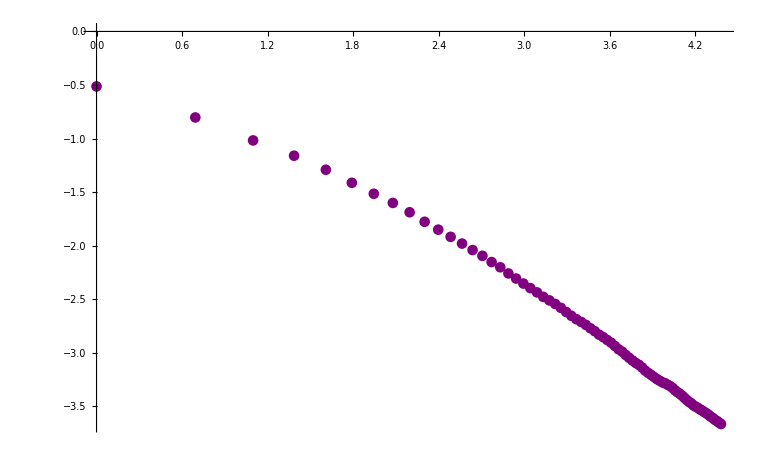

```mathematica
ListPlot[corrtab,Joined->False,AxesOrigin->{0,0},PlotStyle->Directive[PointSize[0.01],Purple],PlotRange->{All,All}]
```

```mathematica
nlm=NonlinearModelFit[Take[corrtab,-30],a*x+b,{a,b},x]
```

FittedModel[0.546322-0.961738 x]

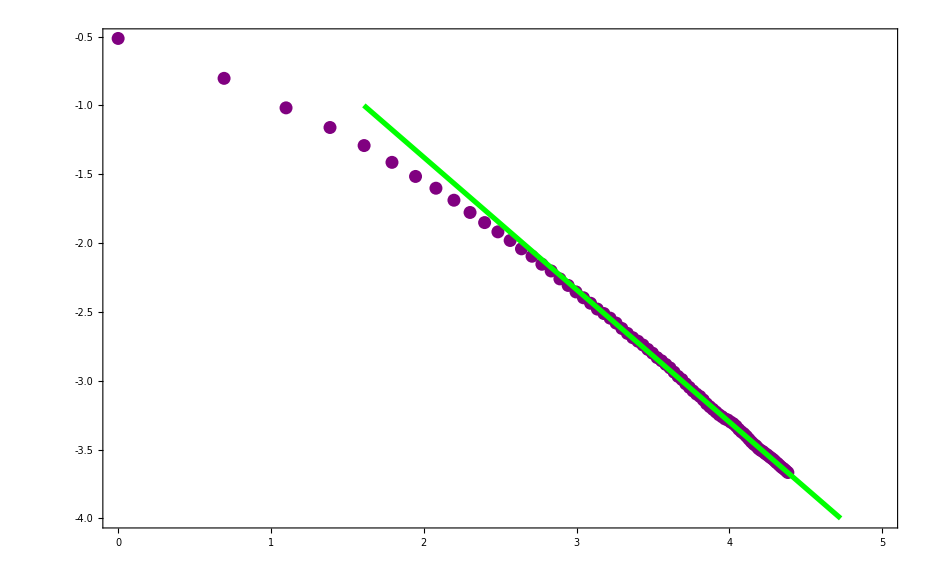

```mathematica
Show[
ListPlot[corrtab,Joined->False,AxesOrigin->{0,0},PlotStyle->Directive[PointSize[0.01],Purple],PlotRange->{All,All}],
Plot[nlm[x],{x,0,60},PlotStyle->Directive[Thickness[0.004],Green],PlotRange->{{0,5},{-4,-1}}],
PlotRange->{{0,5},All},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,5,1,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[-4,0,0.5,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}
]
```

## Generate a system realization and synthetic runoff data

```mathematica
counter=0;Do[If[rH[[i]]≤0,counter+=1],{i,1,Length[rH]}];
If[counter>0,Print["Be careful, negative or zero rain happens ",counter," times in ",Length[rH]," measured points"],Print["Rain is always > 0 -> Ok"]] (* check that rain is non-zero*)

counter=0;Do[If[rD[[i]]≤0,counter+=1],{i,1,Length[rD]}];
If[counter>0,Print["Be careful, negative or zero rain happens ",counter," times in ",Length[rD]," measured points"],Print["Rain is always > 0 -> Ok"]] (* check that rain is non-zero*)
```

Be careful, negative or zero rain happens 20587 times in 26280 measured points

Be careful, negative or zero rain happens 515 times in 1094 measured points

```mathematica
rD=rD+0.1;
counter=0;Do[If[rD[[i]]≤0,counter+=1],{i,1,Length[rD]}];
If[counter>0,Print["Be careful, negative or zero rain happens ",counter," times in ",Length[rD]," measured points"],Print["Rain is always > 0 -> Ok"]] (* check that rain is non-zero*)

rH=rH+0.1;
counter=0;Do[If[rH[[i]]≤0,counter+=1],{i,1,Length[rH]}];
If[counter>0,Print["Be careful, negative or zero rain happens ",counter," times in ",Length[rH]," measured points"],Print["Rain is always > 0 -> Ok"]] (* check that rain is non-zero*)
```

Rain is always > 0 -> Ok

Rain is always > 0 -> Ok

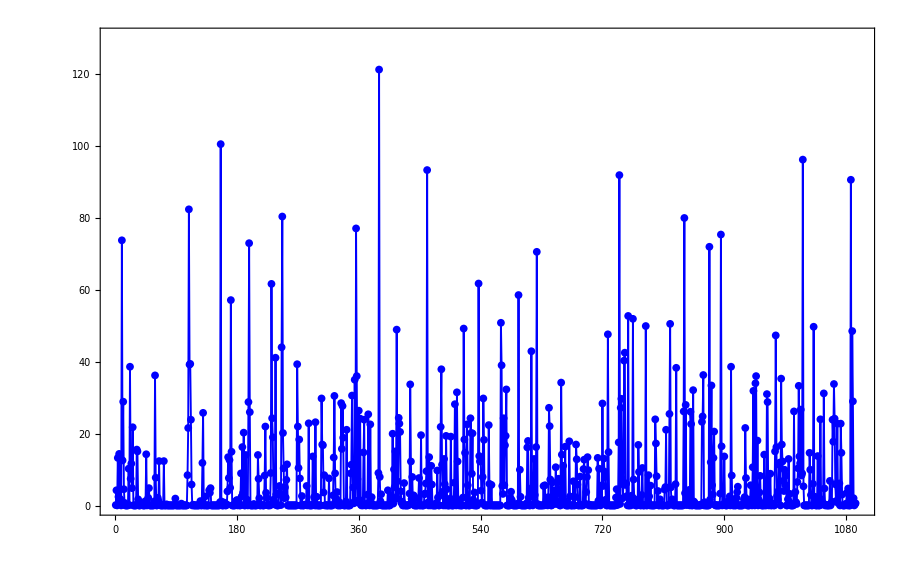

```mathematica
ListPlot[rD,Joined->True,AxesOrigin->{0,0},PlotMarkers->{"●",8},PlotStyle->Directive[Thickness[0.0015],Blue],PlotRange->{{0,1100},{0,130}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,2000,60,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,150,10,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}]
```

```mathematica
365*24 (* hours in 1 year *)
```

8760

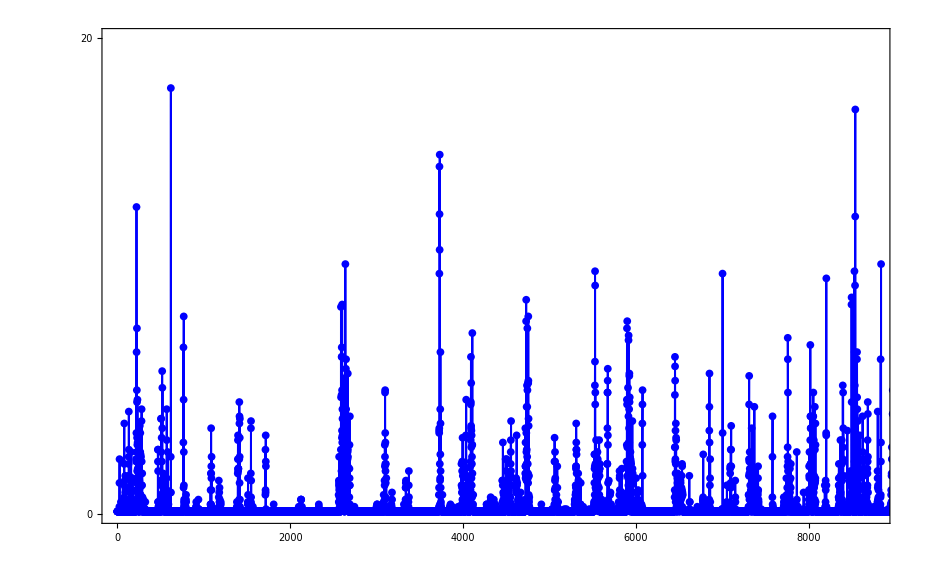

```mathematica
ListPlot[rH,Joined->True,AxesOrigin->{0,0},PlotMarkers->{"●",8},PlotStyle->Directive[Thickness[0.0015],Blue],PlotRange->{{0,8760},{0,20}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,20000,500,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,150,10,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}]
```

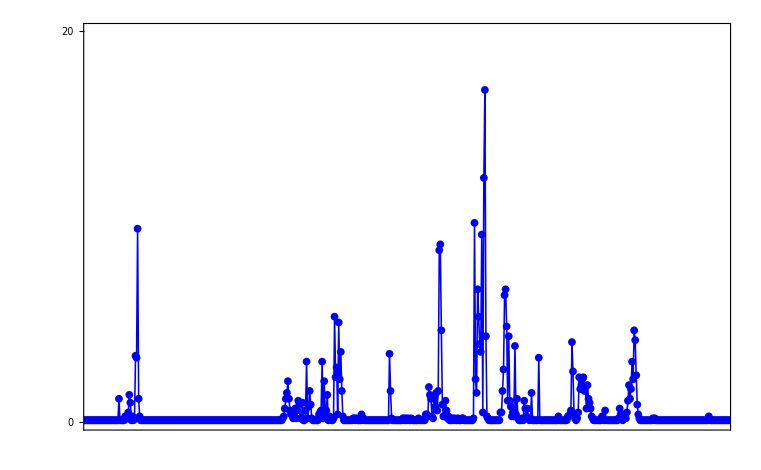

```mathematica
ListPlot[rH,Joined->True,AxesOrigin->{0,0},PlotMarkers->{"●",8},PlotStyle->Directive[Thickness[0.0015],Blue],PlotRange->{{8160,8760},{0,20}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,20000,500,10,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,150,10,5,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}]
```

```mathematica
First[maimaiH[[Range[8160,8760]]]]
Last[maimaiH[[Range[8160,8760]]]]
```

{1985,12,6,22,0,0,0.,0.,0.0233053}

{1985,12,31,22,0,0,0.,0.,0.0440526}

```mathematica
rain=Take[rH,{8160,8760}];
Length[rain]
```

601

```mathematica
Np=601;
n=30;
(* N.B.: (Np-1)/n must be an integer = j*)
If[Mod[(Np-1),n]≠0, Print["The condition (Np-1)/n = integer is not fullfilled !"]];
t=Range[1,601];
T=Last[t]-First[t];
dt=T/(Np-1);
ty=Round[Array[#&,n+1,{1,Np}]];

K=50.;    (* Retention time *)
γ=0.2;    (* Dimensionless noise parameter *)
σ=0.10; (* Measurement noise *)
S=ConstantArray[0.0,Np];    (* System realization *)
St=ConstantArray[0.0,{Np,2}];  (* System realization with time *)
```

```mathematica
ty
```

{1,21,41,61,81,101,121,141,161,181,201,221,241,261,281,301,321,341,361,381,401,421,441,461,481,501,521,541,561,581,601}

```mathematica
S[[1]]=K*rain[[1]];
Do[S[[i]]=S[[i-1]]+dt*(rain[[i-1]]-S[[i-1]]/K)+Sqrt[dt]*Sqrt[γ/K]*S[[i-1]]*RandomVariate[NormalDistribution[]]
,{i,2,Np}]
```

```mathematica
S[[ty]]
```

{5.,4.272,12.4546,13.3858,12.2697,10.0949,7.36122,4.95288,5.87916,3.63621,10.7886,18.3531,43.9012,38.5581,16.2135,23.4028,22.9276,64.3644,44.2486,101.232,93.0212,53.6271,34.7155,48.4088,65.1483,54.3816,72.4946,71.2629,42.7791,27.1912,15.167}

```mathematica
y=S[[ty]]/K*RandomVariate[LogNormalDistribution[0,σ],n+1];
bq=Log[y/rain[[ty]]];
```

```mathematica
(*bq=Log[(1/K)*(S[[All,2]]/rain[[All]])]+σ*RandomVariate[NormalDistribution[],Np];
y=rain[[All]]*Exp[bq];*)

yerr=Table[{{t[[ty[[i]]]],y[[i]]},ErrorBar[2*σ*y[[i]]]},{i,1,Length[y]}];
```

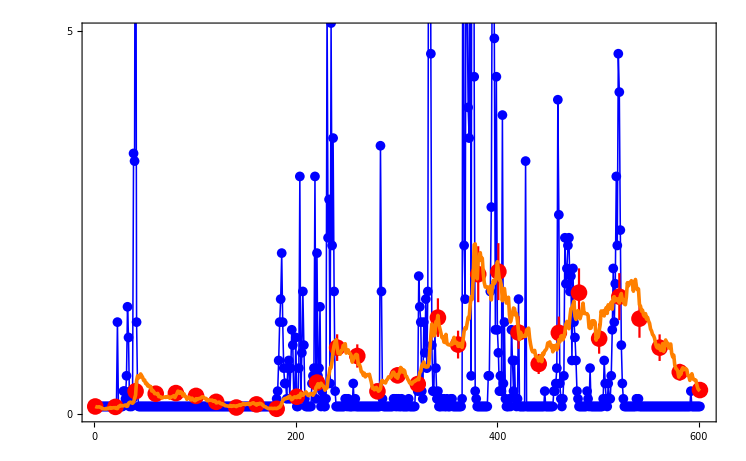

```mathematica
Show[

ListPlot[rain,Joined->True,AxesOrigin->{0,0},PlotMarkers->{"●",10},PlotStyle->Directive[Thickness[0.0015],Blue],PlotRange->{All,All}],
(*Plot[rInt[x],{x,0.17,1667},PlotStyle->{Dashed,Orange,Thickness[0.01]},PlotRange->All],*)

ErrorListPlot[yerr,AxesOrigin->{0,0},PlotStyle->Directive[PointSize[0.016],Red],PlotRange->{{0,1800},{0,10}},PlotRange->{All,All}],

ListPlot[Transpose[{t,S[[All]]/K}],Joined->True,AxesOrigin->{0,0},PlotStyle->Directive[Thickness[0.0035],Orange],PlotRange->{All,All}],

PlotRange->{{0,605},{0,5}},Axes->True,Frame->True,FrameStyle->Directive[Thick,16,Black],FrameTicks->{LinTicks[0,1000,100,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,50,1,4,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}
]
```

## Export data

```mathematica
St[[All,1]]=S[[All]];
St[[All,2]]=t;
```

```mathematica
Export[inputdir<>"\\St_mmH_N601_n30.dat",St]
Export[inputdir<>"\\bq_mmH_N601_n30.dat",bq]
Export[inputdir<>"\\y_mmH_N601_n30.dat",y]
Export[inputdir<>"\\r_mmH_N601_n30.dat",rain]
(*Export[indatdir<>"\\rExt_rr601.dat",rExt]*)
```

C:\Users\ulzegasi\Julia_files\ParInf_HMC\input_data\St_mmH_N601_n30.dat

C:\Users\ulzegasi\Julia_files\ParInf_HMC\input_data\bq_mmH_N601_n30.dat

C:\Users\ulzegasi\Julia_files\ParInf_HMC\input_data\y_mmH_N601_n30.dat

C:\Users\ulzegasi\Julia_files\ParInf_HMC\input_data\r_mmH_N601_n30.dat